```mathematica
l1=(l-1)(l+2);
l2=l(l+1);
df[f_,r_]:=f''[r]-l1(2r f'[r]+(r^2-l2)f[r])/(r^2(r^2-l1))+f[r];
```

```mathematica
findf[l0_, {A_,B_},eps_]:=Module[{fn,r0},
fn[r_]:=df[f,r]/.l->l0;
r0=√l1/.l->l0;
f[r]/.First@NDSolve[{fn[r]==0,f[r0+eps]==A,f''[r0+eps]==2B},f[r],{r,0.5r0,4.5r0}]
];
plotf[f_,l0_]:=Plot[f,{r,0.5 √l1,4.5 √l1}/.l->l0];
```

Из соотношений коэффициентов решения можно получить, что параметрами являются f[r0] и f’’[r0]. Остальные коэффициенты ряда по степеням (r-√l1) выражаются через них или определяются из рекуррентных соотношений.

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

InterpolatingFunction[{{2.64575, 23.8118}}, <>][r]

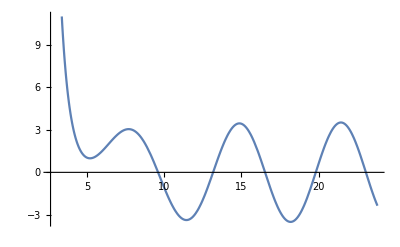

```mathematica
findf[5,{1,1}, 0.00000001]
plotf[%,5]
```

Проверим, что численно полученное решение удовлетворяет заданным граничным условиям и условиям, наложенным на коэффициенты ряда из аналитического их вида.

```mathematica
D[Quiet@findf[5,{1,1},0.00000001],{r,1}]/.{r->0.00000001+√l1/.l->5} 
1/(√(-2+l+l^2))/.l->5//N
```

0.188982

0.188982

```mathematica
D[Quiet@findf[5,{1,1},0.00000001],{r,2}]/2/.{r->0.00000001+√l1/.l->5}
```

1.